# Vaje 6

3. 4. 2025

## 1. Naloga

a) Dana je funkcija . Definirajte funkcijo dveh spremenljivk.

```mathematica
f[x_,y_]:=x^3+y^3-3 x y
```

b) Izračunajte gradient funkcije (par, kjer je na prvem mestu odvod funkcije po x in na drugem mestu odvod funkcije po y). Kdaj je gradient enak 0?

```mathematica
gradf=Grad[f[x,y],{x,y}]
```

{3 x^2-3 y,-3 x+3 y^2}

```mathematica
criticalPoints=Solve[gradf=={0,0},{x,y}]
```

{{x→0,y→0},{x→1,y→1},{x→-(-1)^(1/3),y→(-1)^(2/3)},{x→(-1)^(2/3),y→-(-1)^(1/3)}}

c) Definirajte Hessejevo matriko za funkcijo  in ugotovite, ali je v točki, kjer je gradient funkcije enak 0, dosežen lokalni ekstrem.

```mathematica
HesseMatrix={{D[f[x, y], {x, 2}], D[D[f[x, y], {x, 1}], {y, 1}]}, {D[D[f[x, y], {x, 1}], {y, 1}], D[f[x, y], {y, 2}] }} // MatrixForm
```

(6 x | -3
-3 | 6 y)

```mathematica
HesseInPoint1 = HesseMatrix /. criticalPoints[[1]] (* sedlo *)
```

(0 | -3
-3 | 0)

```mathematica
% // Det
```

-9

```mathematica
HesseInPoint2 = HesseMatrix /. criticalPoints[[2]] (* lokalni minimum *)
```

(6 | -3
-3 | 6)

```mathematica
% // Det
```

27

d) Narišite nivojnico  in označite kritične točke. Vrednost paramtera  naj bo moč spreminjati. Narišite tudi graf funkcije f in označite lokalni minimum.

```mathematica
Manipulate[ContourPlot[f[x,y]==n,{x,-2,2},{y,-2,2},
ContourStyle->Red,
Epilog->{Blue,PointSize[Large],Point[{x, y} /. criticalPoints[[1]]], Blue,PointSize[Large],Point[{x, y} /. criticalPoints[[2]]]}], {n, -5, 5}]
Show[Plot3D[f[x,y],{x,-3,3},{y,-3,3}],Graphics3D[{Blue,Point[{1,1,f[1,1]}]}]]
```

-Graphics3D-

## 2. Naloga

Dana je enačba ploskve .

a) Poiščite precečišča te ploskve s koordinatnimi ravninami.

```mathematica
Solve[x^2+y^2-0^3==1]
```

{{y→-√(1-x^2)},{y→√(1-x^2)}}

```mathematica
Solve[x^2-z^3==1]
```

{{x→-√(1+z^3)},{x→√(1+z^3)}}

```mathematica
Solve[y^2-z^3==1]
```

{{y→-√(1+z^3)},{y→√(1+z^3)}}

b) Narišite ploskev v 3D.

```mathematica
Plot3D[(x^2+y^2 -1)^(1/3),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

## 3. Naloga

Dana je funkcija .

a) Razvijte funkcijo v Taylorjev polinom stopnje 6 okoli točke 0.

```mathematica
f[x_]:=Exp[x] Cos[x^3]
taylorPolynomial=Normal[Series[f[x],{x,0,6}]]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120-(359 x^6)/720

b) Narišite originalno funkcijo in njeno aproksimacijo na intervalu [-2, 2].

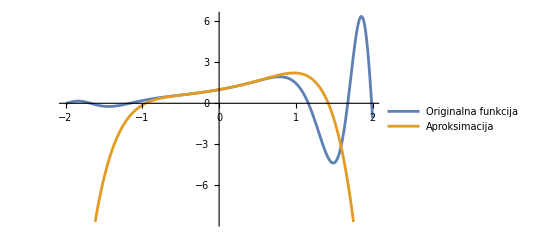

```mathematica
Plot[{f[x],taylorPolynomial},{x,-2,2},PlotLegends->{"Originalna funkcija","Aproksimacija"}]
```

## 4. Naloga

a) Aproksimiraj  s Taylorjevim polinomom stopnje 2 okoli x=0 in oceni napako, ki jo dobiš pri izračunu .

```mathematica
f[x_]:=Cos[x]
taylorCos=Normal[Series[f[x],{x,0,2}]]
approxCos=taylorCos/. {x->0.1}
errorCos=Abs[Cos[0.1]-approxCos]
```

1-x^2/2

0.995

4.16528×10^-6

b) Uporabi Taylorjev polinom stopnje 3 za izračun približka .

```mathematica
f[x_]:=Log[1 - x]
taylorLog=Normal[Series[f[x],{x,0,3}]]
approxLog=taylorLog/. {x->-0.1}
errorLog=Abs[Log[1.1]-approxLog]
```

-x-x^2/2-x^3/3

0.0953333

0.0000231535